```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm_1L_xi/tadpoles/tadpoles/

## Input

```mathematica
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm_1L_xi/tadpoles/tadpoles/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm_1L_xi/tadpoles/tadpoles/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm_1L_xi/tadpoles/tadpoles/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm_1L_xi/tadpoles/tadpoles/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm_1L_xi/tadpoles/tadpoles/input/equivalence_classes.m

## Diagram Backup

## Load

```mathematica
fieldsBorn=<<(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L=<<(NotebookDirectory[]<>"backup/fields/fields1L.m");
fields1Lperm=<<(NotebookDirectory[]<>"backup/fields/fields1Lperm.m");
fields1LBX=<<(NotebookDirectory[]<>"backup/fields/fields1LBX.m");
fields1LTR=<<(NotebookDirectory[]<>"backup/fields/fields1LTR.m");
fields1LSE=<<(NotebookDirectory[]<>"backup/fields/fields1LSE.m");
fields1LTP=<<(NotebookDirectory[]<>"backup/fields/fields1LTP.m");
```

## Paint

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 4 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 5 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 6 aebe/cfdf/egfhghgh.m, 0 diagrams

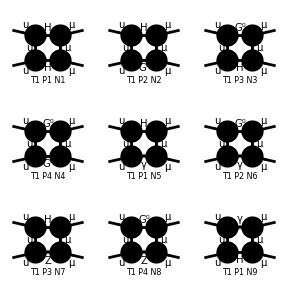

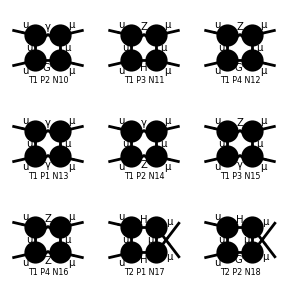

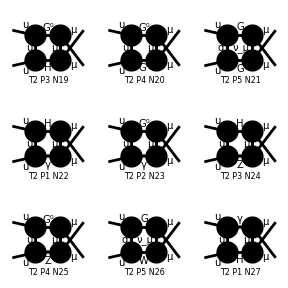

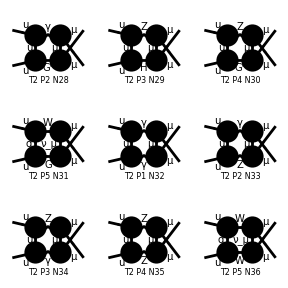

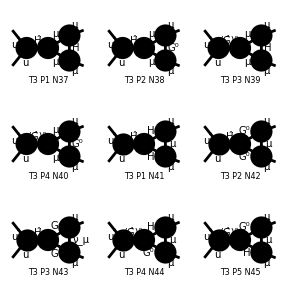

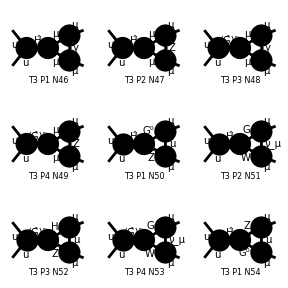

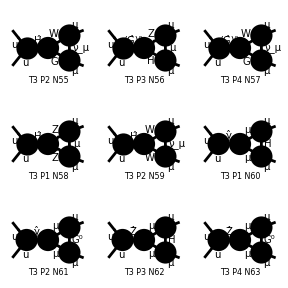

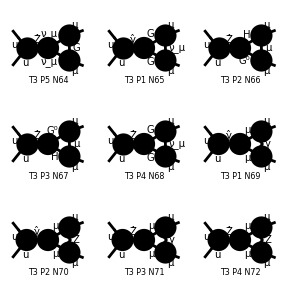

```mathematica
Paint[fields1Lperm];
```

## Coefficient Backup

```mathematica
diagramCoefficients[1]=<<(NotebookDirectory[]<>"final_results/diagramCoefficientsA.m");
timeCoefficients[1]=<<(NotebookDirectory[]<>"final_results/diagramTimeA.m");
diagramCoefficients[2]=<<(NotebookDirectory[]<>"final_results/diagramCoefficientsZ.m");
timeCoefficients[2]=<<(NotebookDirectory[]<>"final_results/diagramTimeZ.m");
diagramCoefficientsRep=<<(NotebookDirectory[]<>"final_results/diagramCoefficientsRep.m");
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
Print["Number of masters: ",Length[masters]];
```

Number of masters: 51

## Set-Up

```mathematica
xiMasters={};
xiMastersW={};
xiMastersZ={};
Do[
If[!FreeQ[masters[[i]],GaugeXi[_]],
xiMasters=AppendTo[xiMasters,i];
If[!FreeQ[Cases[masters[[i]],mz*Sqrt[GaugeXi[_]],Infinity],mz],
xiMastersZ=AppendTo[xiMastersZ,i]
];
If[!FreeQ[Cases[masters[[i]],mw*Sqrt[GaugeXi[_]],Infinity],mw],
xiMastersw=AppendTo[xiMastersW,i]
]
]
,{i,Length[masters]}]
```

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
notNullElements[ll_List]:=Module[{result},
result={};
Do[
If[ll[[i]]=!=0,result=AppendTo[result,i]]
,{i,Length[ll]}];
Return[result]
]
```

## Results

## Z Master

```mathematica
n=8;
m=masters[[n]];
Print["Master:  ",m];
Print["Momenta:  ", userPropagatorMomenta[m[[1]]]];
Print["Masses:  ", userIntegralMasses[m[[1]]]];
```

Master:  userIntegral[A2,{mz √GaugeXi[Q]},0,0,1,0]

Momenta:  {q1,-p1+q1,p2+q1,-p1+p3+q1}

Masses:  {0,0,M1,0}

### Interference 1

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

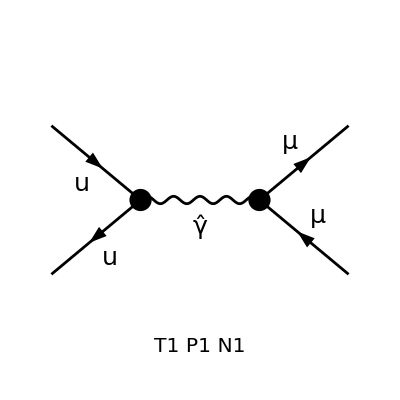

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

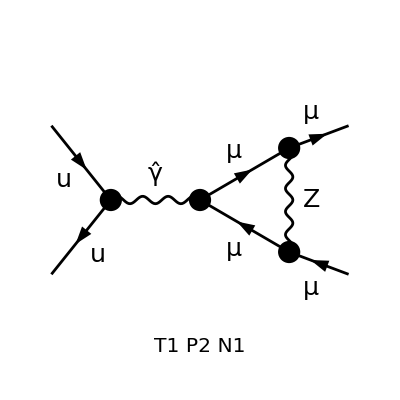

```mathematica
ndiag=70;
Paint[DiagramExtract[fieldsBorn,3],ColumnsXRows->1];
Paint[DiagramExtract[fields1Lperm,ndiag],ColumnsXRows->1];
```

Di seguito è mostrato il contributo al tadpolo dello Z dato dall’interferenza fra i due diagrammi sopra

```mathematica
diagramCoefficients[1][[ndiag,8]]
```

-(ⅈ 2^(-1-d) EL^6 gAl^2 gAu^2 (gZlL^2+gZlR^2) π^-d ((-2+d) s^2+4 s t+4 t^2))/(mz^2 s^2)

### Interference 2

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

-Graphics-

> Top. 1 aebf/cgdg/ghefehfh.m, 0 diagrams

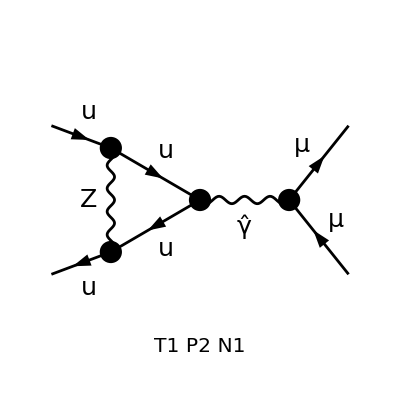

```mathematica
ndiag=118;
Paint[DiagramExtract[fieldsBorn,3],ColumnsXRows->1];
Paint[DiagramExtract[fields1Lperm,ndiag],ColumnsXRows->1];
```

Di seguito è mostrato il contributo al tadpolo dello Z dato dall’interferenza fra i due diagrammi sopra

```mathematica
diagramCoefficients[1][[ndiag,8]]
```

-(ⅈ 2^(-1-d) EL^6 gAl^2 gAu^2 (gZuL^2+gZuR^2) π^-d ((-2+d) s^2+4 s t+4 t^2))/(mz^2 s^2)